```mathematica
MyReIm[x_] := Block[{Z, ZB},
Z = ComplexExpand[x/.E^( I a_):>Cos[a] + I Sin[a]];
ZB =( Z/.I ->-I);
{(Z + ZB)/2, (Z - ZB)/(2 I)}];
```

```mathematica
Eq =MyReIm[((p + I q)(X +I Y)+ a X - I b Y)(X'+ I Y')][[2]]
```

q X X'-b Y X'+p Y X'+a X Y'+p X Y'-q Y Y'

```mathematica
Sub[γ_, β_,a_,c_] :=
{
q -> -c/(4γ+2) Sin[2β],
p ->(-c -2 a + c/(2γ+1 )Cos[2β])/2,
b -> - a-c
};
```

```mathematica
PP[τ_,γ_,β_] := E^( I β)( 1 + I τ)τ^γ;
PPM[τ_,γ_,β_] :=E^( I (β + Pi γ))( 1 - I τ)τ^γ;
PPC[τ_,γ_,β_] := E^( -I β)( 1 - I τ)τ^γ;
PPMC[τ_,γ_,β_] :=E^( -I (β + Pi γ))( 1 + I τ)τ^γ;
```

```mathematica
(* direct substitution *)
XYSub[τ_,γ_,β_]  :=  Block[{Z=FullSimplify[MyReIm[PP[τ,γ,β]],{τ>0, γ>0, -Pi < β < Pi}]},
FullSimplify[{X ->Z[[1]], Y->Z[[2]], X' ->D[Z[[1]],τ],  Y' ->D[Z[[2]],τ]}]
];
```

```mathematica
XYSub[τ,γ,β]
```

{X→τ^γ (Cos[β]-τ Sin[β]),Y→τ^γ (τ Cos[β]+Sin[β]),X'→τ^(-1+γ) (γ Cos[β]-(1+γ) τ Sin[β]),Y'→τ^(-1+γ) ((1+γ) τ Cos[β]+γ Sin[β])}

```mathematica
EqDir = Eq/.XYSub[τ,γ,β]
```

-q τ^(-1+2 γ) (τ Cos[β]+Sin[β]) ((1+γ) τ Cos[β]+γ Sin[β])+a τ^(-1+2 γ) ((1+γ) τ Cos[β]+γ Sin[β]) (Cos[β]-τ Sin[β])+p τ^(-1+2 γ) ((1+γ) τ Cos[β]+γ Sin[β]) (Cos[β]-τ Sin[β])-b τ^(-1+2 γ) (τ Cos[β]+Sin[β]) (γ Cos[β]-(1+γ) τ Sin[β])+p τ^(-1+2 γ) (τ Cos[β]+Sin[β]) (γ Cos[β]-(1+γ) τ Sin[β])+q τ^(-1+2 γ) (Cos[β]-τ Sin[β]) (γ Cos[β]-(1+γ) τ Sin[β])

```mathematica
Eqsub= FullSimplify[EqDir/.Sub[γ, β,a,c] ]
```

0

```mathematica
XYSubMinus[τ_,γ_, β_]  :=  Block[{Z=FullSimplify[MyReIm[PPM[τ,γ,β]],{τ>0, γ>0, -Pi < β < Pi}]},
FullSimplify[{X ->Z[[1]], Y->Z[[2]], X' ->D[Z[[1]],τ],  Y' ->D[Z[[2]],τ]}]
];
```

```mathematica
EqDirMinus = (Eq/.XYSubMinus[τ,γ,β])
```

-q τ^(-1+2 γ) (-τ Cos[β+π γ]+Sin[β+π γ]) (-((1+γ) τ Cos[β+π γ])+γ Sin[β+π γ])+a τ^(-1+2 γ) (-((1+γ) τ Cos[β+π γ])+γ Sin[β+π γ]) (Cos[β+π γ]+τ Sin[β+π γ])+p τ^(-1+2 γ) (-((1+γ) τ Cos[β+π γ])+γ Sin[β+π γ]) (Cos[β+π γ]+τ Sin[β+π γ])-b τ^(-1+2 γ) (-τ Cos[β+π γ]+Sin[β+π γ]) (γ Cos[β+π γ]+(1+γ) τ Sin[β+π γ])+p τ^(-1+2 γ) (-τ Cos[β+π γ]+Sin[β+π γ]) (γ Cos[β+π γ]+(1+γ) τ Sin[β+π γ])+q τ^(-1+2 γ) (Cos[β+π γ]+τ Sin[β+π γ]) (γ Cos[β+π γ]+(1+γ) τ Sin[β+π γ])

```mathematica
EqsubMinus= FullSimplify[EqDirMinus//.Sub[γ,β+ Pi γ,a,c] ]
```

0

```mathematica
a=.;
```

```mathematica
Eqpq =FullSimplify[MyReIm[Exp[I Pi γ] ((p + I q)/.Sub[γ, β,a,c]) -((p+ I q)/.Sub[γ, β+ Pi γ,a,c])]]
```

{(-((2 a+c) (1+2 γ) (-1+Cos[π γ]))+2 c Cos[2 β] (1+2 Cos[π γ]) Sin[(π γ)/2]^2+c Sin[2 β] (Sin[π γ]+Sin[2 π γ]))/(2+4 γ),-1/2 (2 a+c) Sin[π γ]+(c Cos[2 β+(π γ)/2] Sin[(3 π γ)/2])/(1+2 γ)}

```mathematica
Solve[Eqpq[[2]]==0,a]
```

{{a→-(c (1+2 γ-2 Cos[2 β+(π γ)/2] Csc[π γ] Sin[(3 π γ)/2]))/(2 (1+2 γ))}}

```mathematica
ClearAll[γ,β,x,y,a,b,c,A];
```

```mathematica
A[x_,y_] := (a/.Solve[Eqpq[[2]]==0,a][[1]])/.{γ->x,β->y}
```

```mathematica
A[γ,β]
```

-(c (1+2 γ-2 Cos[2 β+(π γ)/2] Csc[π γ] Sin[(3 π γ)/2]))/(2 (1+2 γ))

```mathematica
A1[γ_] := FullSimplify[A[γ,Pi(1-γ)/2]]
```

```mathematica
A1[γ]
```

-(c (1+γ+Cos[π γ]))/(1+2 γ)

```mathematica
FullSimplify[Eqpq/.Solve[Eqpq[[2]]==0,a][[1]]]
```

{(c Sec[(π γ)/2] Sin[(3 π γ)/2] Sin[2 β+π γ])/(1+2 γ),0}

```mathematica
absol = {β->Pi(1-γ)/2, a->FullSimplify[A[γ,Pi(1-γ)/2]]}
```

```mathematica
{β->1/2 π (1-γ),a->-(c (1+γ+Cos[π γ]))/(1+2 γ), b->-c-a}
```

{β→1/2 π (1-γ),a→-(c (1+γ+Cos[π γ]))/(1+2 γ),b→-a-c}

```mathematica
ffn =FullSimplify[(p + I q)/.Sub[γ, 1/2 π (1-γ),-(c (1+γ+Cos[π γ]))/(1+2 γ),c] ]
```

(c (1+ⅇ^(-ⅈ π γ)))/(2+4 γ)

```mathematica
FullSimplify[(p + I q)/.Sub[γ, 1/2 π (1+γ),-(c (1+γ+Cos[π γ]))/(1+2 γ),c] ]
```

(c (1+ⅇ^(ⅈ π γ)))/(2+4 γ)

```mathematica
ClearAll[F];
```

```mathematica
F[w_, γ_] :=
F[w, γ] =
FullSimplify[Cos[Pi γ/2]/(Pi I(2γ+1))Integrate[z^((γ+1)/2)/(w + z),{z,0, Tan[Pi γ/2]^2},GenerateConditions->False]]
```

```mathematica
F[w, γ]
```

-(2 ⅈ Cos[(π γ)/2] Hypergeometric2F1[1,(3+γ)/2,(5+γ)/2,-Tan[(π γ)/2]^2/w] (Tan[(π γ)/2]^2)^((3+γ)/2))/(3 π w+7 π w γ+2 π w γ^2)

```mathematica
F[w_, γ_]  = Numerator[F[w, γ] ]/Factor[Denominator[F[w,γ]]]
```

-(2 ⅈ Cos[(π γ)/2] Hypergeometric2F1[1,(3+γ)/2,(5+γ)/2,-Tan[(π γ)/2]^2/w] (Tan[(π γ)/2]^2)^(3/2+γ/2))/(π w (3+γ) (1+2 γ))

```mathematica
F[w,γ]
```

-(2 ⅈ Cos[(π γ)/2] Hypergeometric2F1[1,(3+γ)/2,(5+γ)/2,-Tan[(π γ)/2]^2/w] (Tan[(π γ)/2]^2)^(3/2+γ/2))/(π w (3+γ) (1+2 γ))

```mathematica
γ=.;
```

```mathematica
Block[{γ0=0.5, τ0, L},
τ0 = Tan[Pi γ0/2];
L = -0.5 - τ0^2;
ComplexPlot3D[F[w,γ0],{w,-L - 0.25 I, L + 0.25I}, PlotRange->{0,1},
PlotLabel->{"Velocity Inside: f(w) for ",Symbol["γ"]==N[γ0]},
PlotLegends->Automatic]
]
```

-Graphics3D-

```mathematica
Block[{γ=0.5, τ0, L},
τ0 = Tan[Pi γ/2];
L = -1 - τ0^2;
ComplexPlot3D[I w^(γ/2)( 1 - Sqrt[w]),{w,-L - L I, L + L I}, PlotRange->{0,5}]
]
```

-Graphics3D-

```mathematica
Block[{γ=0.5, τ0, L},
τ0 = Tan[Pi γ/2];
L = -1 - τ0^2;
ComplexPlot3D[I E^( I Pi γ)w^(γ/2)( 1 + Sqrt[w]),{w,-L - L I, L + L I}, PlotRange->{0,5}]
]
```

-Graphics3D-

```mathematica
Solve[D[w^(γ/2)( 1 - Sqrt[w]),w]==0,w][[1]]
```

{w→γ^2/(1+γ)^2}

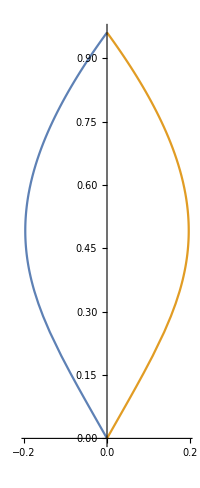

```mathematica
P1 =Block[{γ=1/3, τ0},
τ0 = Tan[Pi γ/2];
ParametricPlot[{ReIm[ I (I τ)^γ( 1 - I τ)],ReIm[ I (-I τ)^γ( 1 + I τ)]},{τ,0, τ0},Exclusions->{τ=0},PlotRange->All]]
```

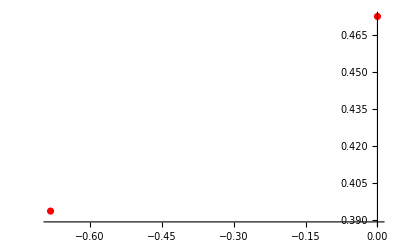

```mathematica
P2 =Block[{γ=1/3, τ0},
t = γ/(γ+1);
ListPlot[{ReIm[I t^γ( 1 -t)],ReIm[I E^( I Pi γ) t^γ(1+t)]},PlotStyle->{Red,Thick},PlotRange->All]]
```

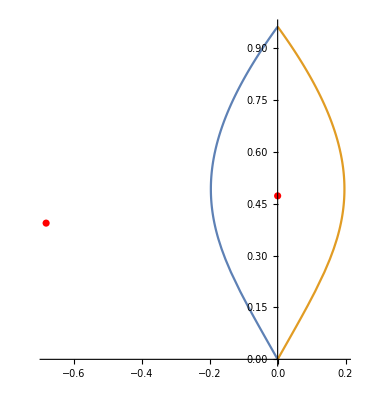

```mathematica
Show[P1, P2,PlotRange->All]
```

```mathematica
ClearAll[γ,β,a,τ];
```

```mathematica
FP[τ_,γ_,β_,  a_, c_] := FullSimplify[With[{b= -c-a},-((p + a-b + I q)//.Sub[γ, β,a,c] )PP[τ,γ,β] + c PPC[τ,γ,β]],{γ,τ,β,a,c} ∈ Reals];
```

```mathematica
ffp=FP[τ,γ,Pi(1-γ)/2, A1[γ], c]
```

-(c ⅇ^(-3/2 ⅈ π γ) τ^γ (-ⅈ+τ+ⅇ^(ⅈ π γ) (-ⅈ+τ)+4 ⅇ^(2 ⅈ π γ) (τ+γ (ⅈ+τ))))/(2 (1+2 γ))

```mathematica
rffp =FullSimplify[MyReIm[ffp][[1]], τ >0]/.τ->Sqrt[z]
```

-(c z^(γ/2) (√z (5+4 γ) Cos[(π γ)/2]+√z Cos[(3 π γ)/2]-2 (1+2 γ+Cos[π γ]) Sin[(π γ)/2]))/(2+4 γ)

```mathematica
ClearAll[G];
```

```mathematica
G[w_, γ_] :=
G[w, γ] =
FullSimplify[Integrate[rffp/(Pi I(w + z)),{z,0,Tan[Pi γ/2]^2},GenerateConditions->False],Tan[Pi γ/2]>0]/.c->1
```

```mathematica
G[w, γ]
```

(4 ⅈ (-((1+2 γ+Cos[π γ]) Hypergeometric2F1[1,(2+γ)/2,(4+γ)/2,-Tan[(π γ)/2]^2/w])/(2+γ)+((2+2 γ+Cos[π γ]) Hypergeometric2F1[1,(3+γ)/2,(5+γ)/2,-Tan[(π γ)/2]^2/w])/(3+γ)) Sin[(π γ)/2] Tan[(π γ)/2]^(2+γ))/(π w (2+4 γ))

```mathematica
γ=.;
x = .;
```

```mathematica
Block[{γ0=1/3, τ0, L,GG},
τ0 = Tan[Pi γ0/2];
L = -0.15 - τ0^2;
GG[x_?NumericQ] := G[w,γ]/.{w->x,γ->γ0};
ComplexPlot3D[GG[x],{x,-L - 0.15 I, L + 0.15I}, PlotRange->{0,0.5},
PlotLabel->{"Velocity Outside: g(w) for ",Symbol["γ"] ==γ0},
WorkingPrecision->20,
Exclusions->{Re[x]==0 || Im[x]==0},
PlotLegends->Automatic]
]
```

-Graphics3D-

```mathematica
Block[{γ0=1/3, τ0, L,GG},
τ0 = Tan[Pi γ0/2];
L = -0.15 - τ0^2;
GG[x_?NumericQ] := F[w,γ]/.{w->x,γ->γ0};
ComplexPlot3D[GG[x],{x,-L - 0.15 I, L + 0.15I}, PlotRange->{0,0.5},
PlotLabel->{"Velocity Inside: f(w) for ",Symbol["γ"] ==γ0},
WorkingPrecision->20,
Exclusions->{Re[x]==0 || Im[x]==0},
PlotLegends->Automatic]
]
```

-Graphics3D-

```mathematica
τ=.
```

```mathematica
FP[τ,γ,Pi(1-γ)/2, A1[γ], c]/.c->1
```

-(ⅇ^(-3/2 ⅈ π γ) τ^γ (-ⅈ+τ+ⅇ^(ⅈ π γ) (-ⅈ+τ)+4 ⅇ^(2 ⅈ π γ) (τ+γ (ⅈ+τ))))/(2 (1+2 γ))

```mathematica
ClearAll[dF];
```

```mathematica
dF[t_, x_] :=FullSimplify[MyReIm[E^(I Pi (1-γ)/2) (τ^(γ-1)  γ-I τ^γ (γ+1))((FP[τ,γ,Pi(1-γ)/2, A1[γ], c]/.c->1)-Cos[Pi γ/2]/(1+2 γ)τ^γ(I + τ))][[1]], {0<γ< 2/3, τ>0}]/.{τ->t, γ->x}
```

```mathematica
τ= .;
```

```mathematica
ClearAll[tt];
```

```mathematica
GG[τ_,γ_] := Integrate[dF[tt,γ],{tt,0,τ},GenerateConditions->False]
```

```mathematica
GG[τ,γ]
```

(τ^(2 γ) (-((1+2 γ) (-1-4 γ+(5+4 γ) τ^2+(1+τ^2) Cos[2 π γ]))-2 τ Cos[π γ] (τ+2 γ τ-2 Sin[π γ])-4 γ τ Sin[π γ]))/(4 (1+2 γ)^2)

```mathematica
H = -((1+2 γ) (-1-4 γ+(5+4 γ) τ^2+(1+τ^2) Cos[2 π γ]))-2 τ Cos[π γ] (τ+2 γ τ-2 Sin[π γ])-4 γ τ Sin[π γ];
(τ^(2 γ) H)/(4 (1+2 γ)^2)
```

```mathematica
FullSimplify[GG[t] - GG[Tan[Pi γ/2]]]
```

1/(8 (1+2 γ)^2)(4 t^(2 γ) (-((1+2 γ) (t^2+(-2 γ+t^2 (3+2 γ)) Cos[π γ]))+2 t (1+γ) (1+4 γ) Sin[π γ])-((1+4 γ) (3+4 γ)-4 (1+2 γ) Cos[π γ]+Cos[2 π γ]) Sec[(π γ)/2]^2 Tan[(π γ)/2]^(2 γ))

```mathematica
DD[t_, x_] := Abs[FullSimplify[((τ^(γ-1)  γ-I τ^γ (γ+1)))((FP[τ,γ,Pi(1-γ)/2, A1[γ], c]/.c->1)-Cos[Pi γ/2]/(1+2 γ)τ^γ(I + τ))^2, {0<γ< 2/3, τ>0}]/.{τ->t, γ->x}]/.Im[γ]->0
```

```mathematica
τ=.;
```

```mathematica
DD[τ,γ]
```

1/4 Abs[(τ^(-1+3 γ) (γ-ⅈ (1+γ) τ) (-ⅈ+τ+2 ⅇ^(ⅈ π γ) τ+ⅇ^(2 ⅈ π γ) (ⅈ+5 τ+4 γ (ⅈ+τ)))^2)/(1+2 γ)^2]

```mathematica
XX=MyReIm[(-ⅈ+τ+2 ⅇ^(ⅈ π γ) τ+ⅇ^(2 ⅈ π γ) (ⅈ+5 τ+4 γ (ⅈ+τ)))]
```

{1/2 (2 τ+4 τ Cos[π γ]+10 τ Cos[2 π γ]+8 γ τ Cos[2 π γ]-2 Sin[2 π γ]-8 γ Sin[2 π γ]),-1+Cos[2 π γ]+4 γ Cos[2 π γ]+2 τ Sin[π γ]+5 τ Sin[2 π γ]+4 γ τ Sin[2 π γ]}

```mathematica
VV=XX.XX
```

1/4 (2 τ+4 τ Cos[π γ]+10 τ Cos[2 π γ]+8 γ τ Cos[2 π γ]-2 Sin[2 π γ]-8 γ Sin[2 π γ])^2+(-1+Cos[2 π γ]+4 γ Cos[2 π γ]+2 τ Sin[π γ]+5 τ Sin[2 π γ]+4 γ τ Sin[2 π γ])^2

```mathematica
SymVV[x_] :=Evaluate[FullSimplify[VV + (VV/.τ->-τ)]/.τ->x]
```

```mathematica
SymVV[τ]
```

4 (1+4 γ+8 γ^2+(15+4 γ (5+2 γ)) τ^2+4 (3+2 γ) τ^2 Cos[π γ]+(-1-4 γ+(5+4 γ) τ^2) Cos[2 π γ])

```mathematica
DDD[τ_,γ_] := 1/(4(1+2 γ)^2) τ^(-1+3 γ) Sqrt[γ^2+(1+γ)^2 τ^2 ]SymVV[τ]
```

```mathematica
ClearAll[Diss];
```

```mathematica
Diss[γ_] :=
Diss[γ] =
FullSimplify[Assuming[{0 < γ < 2/3},Integrate[DDD[τ,γ],{τ,0,Tan[Pi γ/2]},GenerateConditions->False]]]
```

```mathematica
Perim[γ_] :=
Perim[γ] =
FullSimplify[Assuming[{0 < γ < 2/3},Integrate[2Sqrt[γ^2+(1+γ)^2 τ^2 ],{τ,0,Tan[Pi γ/2]},GenerateConditions->False]]]
```

```mathematica
Perim[γ]
```

(γ^2 (-Log[γ]+Log[√(-1-2 γ+(1+γ)^2 Sec[(π γ)/2]^2)+(1+γ) Tan[(π γ)/2]]))/(1+γ)+√(-1-2 γ+(1+γ)^2 Sec[(π γ)/2]^2) Tan[(π γ)/2]

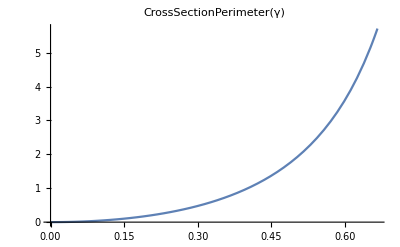

```mathematica
Plot[Perim[γ],{γ,0,2/3},PlotLabel->CrossSectionPerimeter[γ]]
```

```mathematica
ClearAll[τm];
```

```mathematica
Diss[γ]/.{Tan[Pi γ/2]->τm,Cot[Pi γ/2]->1/τm}
```

1/(3 (1+2 γ)^2)(1/τm)^(-3 γ) ((1+4 γ+8 γ^2-(1+4 γ) Cos[2 π γ]) Hypergeometric2F1[-1/2,(3 γ)/2,1+(3 γ)/2,-((1+γ)^2 τm^2)/γ^2]+(3 γ τm^2 (15+4 γ (5+2 γ)+4 (3+2 γ) Cos[π γ]+(5+4 γ) Cos[2 π γ]) Hypergeometric2F1[-1/2,1+(3 γ)/2,2+(3 γ)/2,-((1+γ)^2 τm^2)/γ^2])/(2+3 γ))

```mathematica
Diss[γ]
```

1/(3 (1+2 γ)^2)Cot[(π γ)/2]^(-3 γ) ((1+4 γ+8 γ^2-(1+4 γ) Cos[2 π γ]) Hypergeometric2F1[-1/2,(3 γ)/2,1+(3 γ)/2,-((1+γ)^2 Tan[(π γ)/2]^2)/γ^2]+(3 γ (15+4 γ (5+2 γ)+4 (3+2 γ) Cos[π γ]+(5+4 γ) Cos[2 π γ]) Hypergeometric2F1[-1/2,1+(3 γ)/2,2+(3 γ)/2,-((1+γ)^2 Tan[(π γ)/2]^2)/γ^2] Tan[(π γ)/2]^2)/(2+3 γ))

```mathematica
ClearAll[H];
```

```mathematica
HH[γ_] := (Perim[γ]^3/Diss[γ])^(2/5);
```

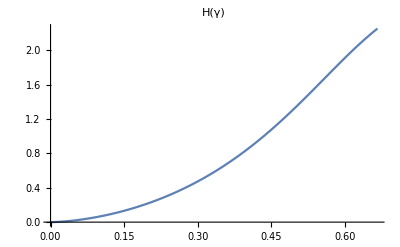

```mathematica
Plot[HH[γ],{γ,0,2/3},PlotLabel->H[γ]]
```

```mathematica
Simplify[HH[γ]/.γ->2/3]
```

((35/3)^(4/5) (5 √237-Log[16]+4 Log[5 √3+√79])^(6/5))/(-23444+1265422 √79)^(2/5)

```mathematica
A1[γ]
```

-(c (1+γ+Cos[π γ]))/(1+2 γ)

```mathematica
Pac[a_, c_] :=1/√(π/3) (c-a) ( -2 a-c)(2 c + a)Exp[-(a ^2 + c^2 + a c)]
```

```mathematica
ClearAll[A1];
```

```mathematica
A1[γ]
```

-(c (1+γ+Cos[π γ]))/(1+2 γ)

```mathematica
PG[x_] := Evaluate[FullSimplify[(D[A1[γ],γ]/.c->1)Integrate[c Pac[A1[γ], c],{c,0,Infinity},GenerateConditions->False],{0 < γ < 2/3}]/.γ->x]
```

```mathematica
PG[γ]
```

-(3 √3 (-1-3 γ+Cos[π γ]) (2+3 γ+Cos[π γ]) (1+2 Cos[π γ]) (1+2 Cos[π γ]+π (1+2 γ) Sin[π γ]))/(8 (1+3 γ (1+γ)+Cos[π γ]+Cos[π γ]^2)^(5/2))

```mathematica
PG[2/3]
```

0

```mathematica
PG[xx]
```

-(3 √3 (-1-3 xx+Cos[π xx]) (2+3 xx+Cos[π xx]) (1+2 Cos[π xx]) (1+2 Cos[π xx]+π (1+2 xx) Sin[π xx]))/(8 (1+3 xx (1+xx)+Cos[π xx]+Cos[π xx]^2)^(5/2))

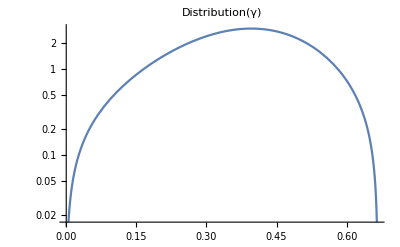

```mathematica
LogPlot[PG[xx],{xx,0,2/3},PlotLabel->Distribution[γ]]
```

```mathematica
Integrate[PG[x],{x,0,2/3}]
```

1

```mathematica
PG[γ_, c_] := FullSimplify[D[A1[γ],γ] Pac[A1[γ], c]]
```

```mathematica
PG[γ, c]
```

(c^4 ⅇ^(-(c^2 (1+3 γ (1+γ)+Cos[π γ]+Cos[π γ]^2))/(1+2 γ)^2) √(3/π) (1+3 γ-Cos[π γ]) (2+3 γ+Cos[π γ]) (1+2 Cos[π γ]) (1+2 Cos[π γ]+π (1+2 γ) Sin[π γ]))/(1+2 γ)^5

```mathematica
ClearAll[c,h]
```

```mathematica
HH1=(r^4 E^(- r^2))/.r ->z^(-6/5)h
```

(ⅇ^(-h^2/z^(12/5)) h^4)/z^(24/5)

```mathematica
HH2 = FullSimplify[-D[z^(-6/5)h,z](√(3/π) (1+3 γ-Cos[π γ]) (2+3 γ+Cos[π γ]) (1+2 Cos[π γ]) (1+2 Cos[π γ]+π (1+2 γ) Sin[π γ]))/(1+2 γ)^5]
```

(6 h √(3/π) (1+3 γ-Cos[π γ]) (2+3 γ+Cos[π γ]) (1+2 Cos[π γ]) (1+2 Cos[π γ]+π (1+2 γ) Sin[π γ]))/(5 z^(11/5) (1+2 γ)^5)

```mathematica
1/Integrate[r^4 E^(-r^2), {r,0,Infinity}]
```

8/(3 √π)

```mathematica
Pdf[x_, y_, t_]:=FullSimplify[HH1 HH2/Integrate[r^4 E^(-r^2), {r,0,Infinity}]]/.{γ->x,h->y, z->t}
```

```mathematica
Pdf[x,y,z]
```

(16 √3 ⅇ^(-y^2/z^(12/5)) y^5 (1+3 x-Cos[π x]) (2+3 x+Cos[π x]) (1+2 Cos[π x]) (1+2 Cos[π x]+π (1+2 x) Sin[π x]))/(5 π (1+2 x)^5 z^7)

```mathematica
PerimPDF[z_] := NIntegrate[Pdf[γ,HH[γ],z],{γ,0,2/3}]
```

```mathematica
PerimPDF[1.]
```

0.481998

```mathematica
PerimInterp = Interpolation[ParallelTable[{u,Log[PerimPDF[E^u]]},{u,-15,3,0.1}]]
```

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

«6 more identical outputs»

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
PerimInterp[1]
```

-5.80937

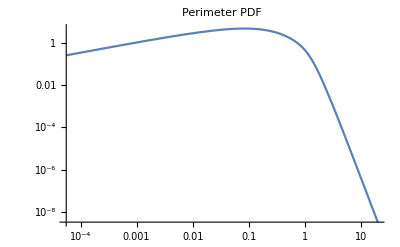

```mathematica
LogLogPlot[Exp[PerimInterp[Log[u]]],{u,Exp[-15],Exp[3]},PlotLabel->"Perimeter PDF",PlotRange->All]
```

```mathematica
dI[t_, x_] :=FullSimplify[E^(I Pi (1-γ)/2)  τ^γ (1 - I τ)E^(I Pi (1-γ)/2) (τ^(γ-1)  γ-I τ^γ (γ+1))((FP[τ,γ,Pi(1-γ)/2, A1[γ], c]/.c->1)-Cos[Pi γ/2]/(1+2 γ)τ^γ(I + τ)), {0<γ< 2/3, τ>0}]/.{τ->t, γ->x}
```

```mathematica
dI[τ, γ]
```

-(ⅇ^(-5/2 ⅈ π γ) τ^(3 γ) (ⅈ+τ) (τ+γ (ⅈ+τ)) (-ⅈ+τ+2 ⅇ^(ⅈ π γ) τ+ⅇ^(2 ⅈ π γ) (ⅈ+5 τ+4 γ (ⅈ+τ))))/(2 (τ+2 γ τ))

```mathematica
II[γ_] := Evaluate[FullSimplify[Integrate[Expand[(dI[τ, γ]  + dI[-τ,γ])],{τ,0, Tan[Pi γ/2]}],{0 <γ < 2/3}]]
```

```mathematica
II[γ]
```

(ⅇ^(-5/2 ⅈ π γ) (-3-6 γ-2 ⅇ^(ⅈ π γ) (2+3 γ)+ⅇ^(4 ⅈ π γ) (3+6 γ)-3 ⅇ^(3 ⅈ π γ) (1+2 γ) (5+12 γ)+6 ⅇ^(5 ⅈ π γ) (1+γ (5+6 γ))+6 ⅇ^(6 ⅈ π γ) (1+γ (5+6 γ))+2 ⅇ^(2 ⅈ π γ) (2+3 γ) (3+4 γ (5+6 γ))+ⅇ^(7 ⅈ π γ) (13+6 γ (7+6 γ))-2 ⅇ^(8 ⅈ π γ) (9+2 γ (32+9 γ (7+4 γ)))) Cot[(π γ)/2]^(-3 (1+γ)))/(3 (-1+ⅇ^(ⅈ π γ))^3 (1+2 γ) (1+3 γ) (2+3 γ))

```mathematica
Ans = (ⅇ^(-5/2 ⅈ π γ) Cot[(π γ)/2]^(-3 (1+γ)))/( 3 (-1+ⅇ^(ⅈ π γ))^3 (1+2 γ) (1+3 γ) (2+3 γ))(
-3-6 γ-2 ⅇ^(ⅈ π γ) (2+3 γ)+
ⅇ^(4 ⅈ π γ) (3+6 γ)-3 ⅇ^(3 ⅈ π γ) (1+2 γ) (5+12 γ)+
6 ⅇ^(5 ⅈ π γ) (1+γ (5+6 γ))+
6 ⅇ^(6 ⅈ π γ) (1+γ (5+6 γ))+
2 ⅇ^(2 ⅈ π γ) (2+3 γ) (3+4 γ (5+6 γ))+
ⅇ^(7 ⅈ π γ) (13+6 γ (7+6 γ))-
2 ⅇ^(8 ⅈ π γ) (9+2 γ (32+9 γ (7+4 γ)))
) ;
```

```mathematica
CC=Re[9/(5Pi^2)NIntegrate[Block[{X = II[γ], Y =(Perim[γ]^3/Diss[γ])^(2)},X X* Y],{γ,0,2/3},WorkingPrecision->20]]
```

4.0472344474366802002

```mathematica
(*Re[Integrate[Block[{X = II[γ], Y =(Perim[γ]^3/Diss[γ])^(2)},X X* Y],{γ,0,2/3}]]*)
```

```mathematica
CC^(1/8)
```

1.1909534733621251683

```mathematica
ClearAll[t];
```

```mathematica
DA[γ_,t_] := Evaluate[Block[{X,Y},
 {X,Y}= FullSimplify[MyReIm[E^(I Pi (1-γ)/2)  (t^γ  +I t^(γ+1))],{t>0, γ>0}];
2 X D[Y,t]]]
```

```mathematica
DA[γ,t]
```

2 t^γ (-t Cos[(π γ)/2]+Sin[(π γ)/2]) (t^γ Sin[(π γ)/2]+t^(-1+γ) γ (Cos[(π γ)/2]+t Sin[(π γ)/2]))

```mathematica
MyA[γ_] := Evaluate[FullSimplify[Integrate[DA[γ,t],{t,0,Tan[Pi γ/2]},GenerateConditions->False]]]
```

```mathematica
MyA[γ]
```

Tan[(π γ)/2]^(1+2 γ)/(1+2 γ)

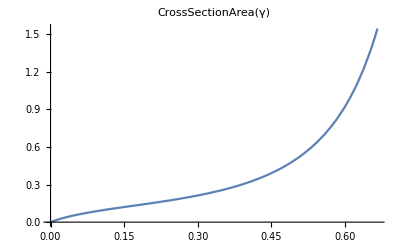

```mathematica
Plot[MyA[γ],{γ,0,2/3},PlotLabel->CrossSectionArea[γ]]
```